Your Title Here

```mathematica
h=1;w=0.5;ry=0.1;L=0.35;z=0.15;δ1=0.1;δ2=0.5;
```

```mathematica
column=Graphics[{Thick,
(*COLUMN*)
Line[{{#,0},{#,h}}]&/@{0,w},
Circle[{0.5*w,h},{0.5*w,ry},{0,π}],Circle[{0.5*w,0},{0.5*w,ry},{π,2*π}],

(*ARROWS*)
{Arrowheads@0.05,
(*FEED*)Arrow[{{-L,0.5*h},{0,0.5*h}}],
(*COMP*)
Arrow[{{0.5*w,h+ry},{0.5*w,h+ry+z},{w+L,h+ry+z},{w+L,h}}],Arrow[{{w+L-0.1,h-0.1},{w,h-0.1}}],Arrow[{{w+L+0.1,h-0.1},{w+L+0.1+2*δ1,h-0.1}}],
(*Reboiler*)
{Arrowheads@{-0.05,0.05},Arrow[{{0.25*w,-0.07},{0.25*w,-δ2},{w+L+2*δ1,-δ2}}]},
Arrow[{{0.75*w,0-ry},{0.75*w,-δ2+0.1}}]},

{EdgeForm@Thick,FaceForm@None,Circle[{w+L,h-0.1},0.1]},
Text[Style["C",18],{w+L,h-0.1}],
{EdgeForm@Thick,White,Disk[{0.75*w,-δ2},0.1]},
Text[Style["R",18],{0.75*w,-δ2}]
},ImageSize->{500,400}];
```

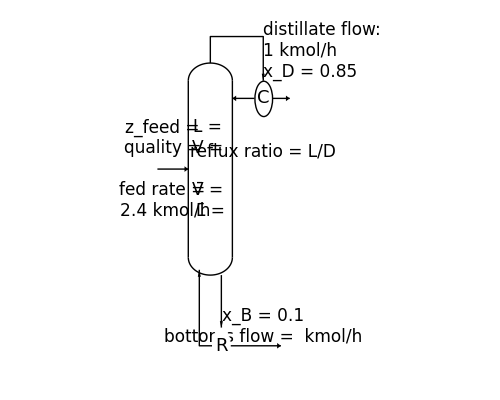





```mathematica
Show[column,PlotRange->{{-1,1.5},All},
Epilog->{
Text[Style[Column[{
Row@{Style["L",Italic]," = "},
Row@{Style["V",Italic]," = "},Spacer@25,
Row@{OverBar[Style["V",Italic]]," = "},
Row@{OverBar[Style["L",Italic]]," = "}
}],17],{0.5*w,0.5*h}],
Text[Style[Column[{
"distillate flow:",
Row@{1," kmol/h"},
Row@{Subscript[Style["x",Italic],"D"]," = ",0.85}
},Center],17],{w+L,h},{-1.5,-0.55}],
Text[Style[Row@{"reflux ratio = ",Style["L",Italic]/Style["D",Italic]},17],{w+L,0.6*h}],
Text[Style[Column[{
Row@{Subscript[Style["x",Italic],"B"]," = ",0.1},
Row@{"bottoms flow = "," kmol/h"}
},Center],17],{w+L,-δ2},{-0.2,-1.5}],
Text[Style[Column[{
Row@{Subscript[Style["z",Italic],"feed"]," = "},
Row@{"quality = "},Spacer@10,
Column[{"fed rate = ",Row@{2.4," kmol/h"}}]
}],17],{-0.75*L,0.5*h}]
}]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX